First of  all this is based on the book Using Mathematica for quantum mechanics by Roman Schmied, this is simply exercise 2.2

### 1.For the First part we know that the ϕ_n form a complete orthonormal basis therefore ∑_(n=1)^∞ nn=1, so we end up with P_∞(x,y)=xy=δ(x-y)

### 2. So with finite n, we could simply use P_n_max(x,y)=∑_(n=1)^n_max xnny= 2 ∑_(n=1)^n_max Sin(n π x) Sin(n π y) our variable for n_max will be m

```mathematica
m=10
```

10

```mathematica
10
```

10

```mathematica
P[x_,y_]=2*Sum[Sin[n*π*x]*Sin[n*π*y],{n,m}];
```

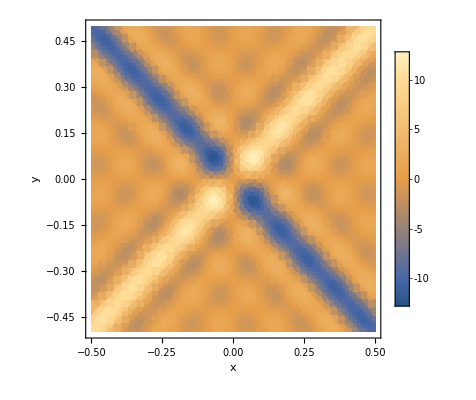

```mathematica
DensityPlot[P[x,y],{x,-0.5,0.5},{y,-0.5,0.5},PlotRange->All,PlotPoints->2*m,FrameLabel->{x,y},PlotLegends->Automatic]
```

### 3. The function Π=∑_(n=1)^∞ nn is the proyector onto the computational subspace, and P is it’s representation in coordinate space, when we truncate it , we leave it with finite spatial resolution